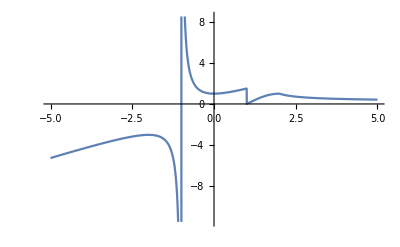

```mathematica
f[x_]:=(1-x^3)/(1-x^2)/;x<1
f[x_]:=Sin[(π*(x-1))/2]/;1≤x≤2
f[x_]:=1/Log[E(x-1)]/;x>2
Plot[f[x],{x,-5,5}]
```

```mathematica
Solve[f[x]==0.75,x]
```

{{x→1.53989}}